## Connexion DLL

## DLL

```mathematica
Clear[pathToDll]
```

```mathematica
Needs["NETLink`"];
```

```mathematica
InstallNET[];
```

```mathematica
(*pathToDll="C:\\Users\\Clem\\Documents\\ESGI\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";*)
pathToDll="D:\\git\\projet_annuel_ibd3a\\C++_lib\\Dll-Machine-Learning\\x64\\Debug\\Dll-Machine-Learning.dll";
```

```mathematica
return42ExternFunc=DefineDLLFunction["return42",pathToDll,"int",{}];
```

```mathematica
return42ExternFunc[]
```

42

## Définitions Méthodes C++

```mathematica
Clear[createLinearModel, linearFitClassificationRosenblatt, linearClassify, linearCreateAndFitRegression, linearPredict];
```

### Perceptron Linéaire

#### Création modèle

```mathematica
createLinearModel = DefineDLLFunction["createLinearModel", pathToDll, "System.IntPtr", {"int", "int"}];
```

#### Classification Linéaire Rosenblatt

```mathematica
linearFitClassificationRosenblatt = DefineDLLFunction["linearFitClassificationRosenblatt", pathToDll, "int", {"System.IntPtr", "double[]", "int", "int", "double[]", "int", "int", "double"}];
```

```mathematica
linearClassify =  DefineDLLFunction["linearClassify", pathToDll, "double", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

#### Régression linéaire

```mathematica
linearCreateAndFitRegression = DefineDLLFunction["linearCreateAndFitRegression", pathToDll, "void", {"System.IntPtr", "double[]", "int", "int", "double[]","int"}];
```

```mathematica
linearPredict = DefineDLLFunction["linearPredict", pathToDll, "void", {"System.IntPtr", "double[]", "int", "double[]", "int"}];
```

#### Perceptron Multi - Couches

```mathematica
createMlp=DefineDLLFunction["createMlp",pathToDll,"System.IntPtr",{"int[]","int"}];
```

```mathematica
classify=DefineDLLFunction["classify",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
fitClassification=DefineDLLFunction["fitClassification",pathToDll,"void",{"System.IntPtr","double[]","int","int","double[]","int"}];
```

```mathematica
predict=DefineDLLFunction["predict",pathToDll,"void",{"System.IntPtr","double[]","int"}];
```

```mathematica
eraseMlp=DefineDLLFunction["eraseMlp",pathToDll,"void",{"System.IntPtr"}];
```

```mathematica
getOutputsforRegression=DefineDLLFunction["getOutputsforRegression",pathToDll,"double",{"System.IntPtr"}];
```

#### NAIVE RBF

```mathematica
createNaiveRbfModel=DefineDLLFunction["createNaiveRbfModel",pathToDll,"System.IntPtr",{"int","double","double[]","int","double[]"}];
```

```mathematica
naiveRbfGetResponse=DefineDLLFunction["naiveRbfGetResponse",pathToDll,"void",{"System.IntPtr","double","double[]","int","double[]","double[]","int"}];
```

#### RBF

```mathematica
createRbfModel= DefineDLLFunction["createRbfModel",pathToDll,"System.IntPtr",{"int","double","double[]","int","double[]","int"}];
```

```mathematica
getRbfResponse=DefineDLLFunction["getRbfResponse",pathToDll,"void",{"System.IntPtr","double","double[]","int","double[]","double[]","int"}];
```

```mathematica
lloydAlgorithm=DefineDLLFunction["lloydAlgorithm",pathToDll,"void",{"System.IntPtr","double[]","int","int","int"}];
```

```mathematica
showRepresentative=DefineDLLFunction["showRepresentative",pathToDll,"void",{"System.IntPtr","int"}];
```

## Cas de tests

### Simple Linéaire

```mathematica
Clear[a,b,c,positivePoints, negativePoints, f];
```

```mathematica
a = RandomInteger[{-5; 5}];
b= RandomInteger[{-5; 5}];
c= RandomInteger[{-5; 5}];
```

```mathematica
f[x_] := -a/b*x+c/b
```

```mathematica
positivePoints = Table[x= RandomReal[{-5, 5}]; {x, f[x] + RandomReal[{0.5, 2}]}, {i,1, 3}]
```

{{0.637883,1.2121},{-4.68017,1.44543},{4.0227,1.48276}}

```mathematica
negativePoints = Table[x = RandomReal[{-5, 5}];
{x, f[x]-RandomReal[{0.5, 2 }]}, {i,1,3}]
```

{{3.87044,-1.40251},{4.28967,-0.89299},{-1.59517,-1.60488}}

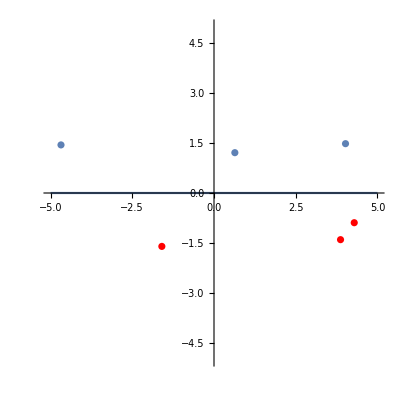

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],
ListPlot[negativePoints, PlotStyle->Red],
ListPlot[positivePoints]]
```

```mathematica
Clear[X, Y, model, Xtest, Ytest, Xtest2, positive, negative]
```

```mathematica
X = Flatten[{positivePoints, negativePoints}]
```

{0.637883,1.2121,-4.68017,1.44543,4.0227,1.48276,3.87044,-1.40251,4.28967,-0.89299,-1.59517,-1.60488}

```mathematica
Y = {1, 1, 1, -1, -1, -1}
```

{1,1,1,-1,-1,-1}

```mathematica
{1,1,1,-1,-1,-1}
```

{1,1,1,-1,-1,-1}

```mathematica
Xtest = {-4.059661874733521,3.88961785568734}
Ytest = {1}
```

{-4.05966,3.88962}

{1}

### Utilisation méthodes

```mathematica
model = createLinearModel[2,1];
```

NET::netexcptn: A .NET exception occurred: System.EntryPointNotFoundException: Impossible de trouver le point d'entrée 'createLinearModel' dans la DLL 'D:\git\projet_annuel_ibd3a\C++_lib\Dll-Machine-Learning\x64\Debug\Dll-Machine-Learning.dll'.
   à Wolfram.NETLink.DynamicDLLNamespace.DLLWrapper38.createLinearModel(Int32 , Int32 ).

```mathematica
linearFitClassificationRosenblatt[model, X, 12, 2, Y, 1, 1000, 0.1];
```

NET::methodargs: Improper arguments supplied for method named linearFitClassificationRosenblatt.

```mathematica
linearClassify[model, Xtest, 2, Ytest, 1];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

```mathematica
Xtest2 = Partition[Flatten[Table[{i,j},{i, -5, 5, 0.2}, {j, -5, 5, 0.2}]], 2];
```

```mathematica
positive = Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== 1&];
negative =Select[Xtest2,linearClassify[model, #,2, Ytest,1 ]== -1&];
```

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

NET::methodargs: Improper arguments supplied for method named linearClassify.

General::stop: Further output of NET::methodargs will be suppressed during this calculation.

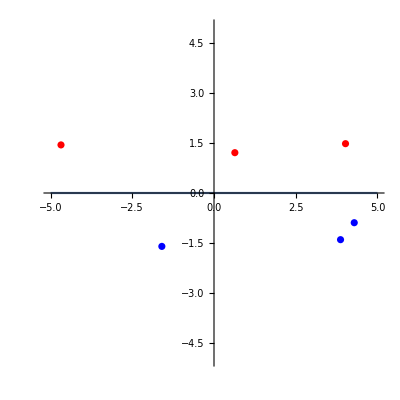

```mathematica
Show[Plot[f[x], {x,-5, 5}, PlotRange->{-5,5},
AspectRatio->1],ListPlot[positive, PlotStyle->Red], ListPlot[negative, PlotStyle->Blue], ListPlot[negativePoints, PlotStyle->Blue, PlotStyle->Thick],
ListPlot[positivePoints, PlotStyle->Red, PlotStyle->Thick]]
```